```mathematica
II[ρ_,μ_, β_]:=Evaluate[Integrate[Sin[ρ s]/(ρ s) s^(μ-β-1),{s,0,Infinity},GenerateConditions->False]]
```

```mathematica
II[r/Sqrt[ν t],1.256,0.813]
```

2.75507/((r^2/(t ν))^0.2215)

```mathematica
JJ[ρ_,μ1_,W1_,A1_, μ2_, W2_,A2_, β_, Ads_]:=
Ads β/4 (W1/(W1 + W2) A1 II[ρ,μ1,β] -W2/(W1 + W2)A2  II[ρ,μ2,β]);
```

```mathematica
JJ[ρ,1.256,128927,13851.157,1.200,345312,15988.304,0.813, 3.568 10^(-4)]//Expand
```

0.752351/((ρ^2)^0.2215)-2.59419/((ρ^2)^0.1935)

```mathematica
Exp[Log[0.752351133293951/2.5941903131207114] /((0.2215-0.1935)*2)]
```

2.51382×10^-10

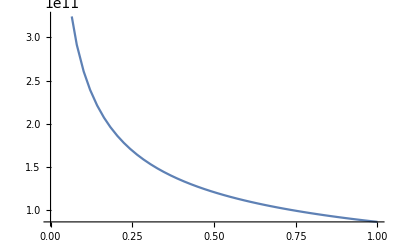

```mathematica
Plot[JJ[ρ,1.274,12912,16410.389,1.197,34355,15460.604,0.81],{ρ,0,10^(-15)}]
```